# PDcode Association test.

--Jason, April 2025. The purpose of this notebook is to see if we can quickly recognize PD codes as Association keys instead of calling Jones to identify them. So we’re going to try to build the PD association first. In this version, we’re trying to recognize individual summands, so we’re going to build the lookup table separately.

```mathematica
Exit[]
```

```mathematica
Needs["PM`"]
UninstallPackages[$PM,{"KnoodleLink"}];  (* comment out to load w/o recompiling *)
ClearAllCache[$PM]; (* comment out to load w/o recompiling *)
LoadPackages[{"Geometries","KnoodleLink"}];
```

Deleting package KnoodleLink.

Deleting installation path.

Deleting files {/Users/jasoncantarella/PackageSources_2025-04-29T19-35-58/PackageSources/KnoodleLink/Link2DObject_Library.nb,/Users/jasoncantarella/PackageSources_2025-04-29T19-35-58/PackageSources/KnoodleLink/MatrixQuadTreeObject_Library.nb,/Users/jasoncantarella/PackageSources_2025-04-29T19-35-58/PackageSources/KnoodleLink/PlanarDiagramObject_Library.nb}

WARNING: LTemplate has not yet been tested with Mathematica 14.2.1.
The latest supported Mathematica version is 12.3.1.
Please report any issues you find to szhorvat at gmail.com.

Updating package KnoodleLink...

/Users/jasoncantarella/PackageSources_2025-04-29T19-35-58/PackageSources/KnoodleLink/LibrarySources/Link2DObject/

/Users/jasoncantarella/PackageSources_2025-04-29T19-35-58/PackageSources/KnoodleLink/LibrarySources/MatrixQuadTreeObject/

/Users/jasoncantarella/PackageSources_2025-04-29T19-35-58/PackageSources/KnoodleLink/LibrarySources/PlanarDiagramObject/

Exporting library Link2DObject to /Users/jasoncantarella/Library/Wolfram/Applications/KnoodleLink/LibraryResources/Source.

Names of functions in library Link2DObject are made public.

Exporting library MatrixQuadTreeObject to /Users/jasoncantarella/Library/Wolfram/Applications/KnoodleLink/LibraryResources/Source.

Names of functions in library MatrixQuadTreeObject are made public.

Exporting library PlanarDiagramObject to /Users/jasoncantarella/Library/Wolfram/Applications/KnoodleLink/LibraryResources/Source.

Names of functions in library PlanarDiagramObject are made public.

/Users/jasoncantarella/PackageSources_2025-04-29T19-35-58/PackageSources/Repositories/Knoodle

Set::write: Tag CrossingCount in SyntaxInformation[CrossingCount] is Protected.

Current directory is: /Users/jasoncantarella/Library/Wolfram/Applications/KnoodleLink/LibraryResources/Source

Unloading library Link2DObject ...

Generating library code ...

Compiling library code ...

Compilation done. Time elapsed = 6.23935

Current directory is: /Users/jasoncantarella/Library/Wolfram/Applications/KnoodleLink/LibraryResources/Source

Unloading library MatrixQuadTreeObject ...

Generating library code ...

Compiling library code ...

Compilation done. Time elapsed = 2.28734

Current directory is: /Users/jasoncantarella/Library/Wolfram/Applications/KnoodleLink/LibraryResources/Source

Unloading library PlanarDiagramObject ...

Generating library code ...

Compiling library code ...

Compilation done. Time elapsed = 24.6674

/Users/jasoncantarella/PackageSources_2025-04-29T19-35-58/PackageSources/Repositories/Knoodle

```mathematica
ClearAll[ExtractUniquePDCodes];ExtractUniquePDCodes[fname_,knownPDCodes_]:= Block[{
fileString,knotStrings,observedPDCodes=<||>,
importTiming,splitTiming,pdCodes,knots,parseTiming,debug = False,tentativeID,rattleVersion},
If[debug,Print["Working on file..."<>fname]];
{importTiming,fileString} = AbsoluteTiming[Import[fname,"String"]];
If[StringLength[fileString]>0,
{splitTiming,knotStrings} = AbsoluteTiming[StringSplit[fileString,"k"]];
parseTiming = 
AbsoluteTiming[
Function[s,
If[s != "\n",
(* The knot is nontrivial *)
pdCodes = (Map[ToExpression,StringExtract[#,2;;-2,All ],{2}] &) /@ (Rest@StringSplit[s,"s"]);
If[debug,Print["Split knot into "<>ToString[Length[pdCodes]]<>" components"]];
Function[pdCode,
If[Not[KeyExistsQ[knownPDCodes,pdCode]]∧
 Not[KeyExistsQ[observedPDCodes,pdCode]],
tentativeID = KnotIdentify[PlanarDiagram[pdCode]];
If[Or[tentativeID ==Nothing,MatchQ[tentativeID,_Or]],
AssociateTo[observedPDCodes,Echo[pdCode->UnknownKnotSymbol[pdCode]]];
];
If[MatchQ[tentativeID,_KnotSymbol],
AssociateTo[observedPDCodes,pdCode->tentativeID]
]
] 
]/@ pdCodes;
]
] /@ knotStrings
][[1]];
If[debug,Print["complete. File import: "<>ToString[importTiming]<>"\n Splitting: "<>ToString[splitTiming]<>"\n Parsing: "<>ToString[parseTiming]<>"\n Number of unique PD codes: "<>ToString[Length[Keys[observedPDCodes]]]]];
];
observedPDCodes
]
```

```mathematica
mediumDirs=FileNames["/users/jasoncantarella/clisbytreesap/data/pfruns-medium/*"];
```

```mathematica
(*mediumObservations=<||>;
Block[{timing,files,newCodes},
timing = AbsoluteTiming[
files = Flatten[Table[FileNames[dir<>"/PD*"],{dir,mediumDirs}]];
Do[
newCodes = ExtractUniquePDCodes[file,mediumObservations];
mediumObservations = Merge[{mediumObservations,newCodes},First];
PrintTemporary["Processed file "<>file<>" unique codes now "<>ToString[Length[mediumObservations]]],
{file,files}
]
][[1]];
Print["Time elapsed: "<>ToString[timing]<>"\nTotal number of unique pd codes: "<>ToString[Length[mediumObservations]]]
];*)
```

```mathematica
largeDirs=FileNames["/users/jasoncantarella/clisbytreesap/data/pfruns-large/*"];
```

```mathematica
(*largeObservations2 = mediumObservations;
Block[{timing,files,newCodes},
timing = AbsoluteTiming[
files = Flatten[Table[FileNames[dir<>"/PD*"],{dir,largeDirs}]];
Do[
newCodes = ExtractUniquePDCodes[file,largeObservations2];
largeObservations2 = Merge[{largeObservations2,newCodes},First];
PrintTemporary["Processed file "<>file<>" unique codes now "<>ToString[Length[largeObservations2]]],
{file,files}
]
][[1]];
Print["Time elapsed: "<>ToString[timing]<>"\nTotal number of unique pd codes: "<>ToString[Length[largeObservations2]]]
];*)
```

We’re now ready to convert these to the new format. Knots are going to be associations between KnotSymbols and counts of the number of connect summands of that type.

```mathematica
ClearAll[ResolveKnot];
ResolveKnot[u_UnknownKnotSymbol]:=Block[{ki,ki2,pd},
ki = KnotIdentify /@ (MonotoneRattle[PlanarDiagram@First[u],10]);
If[MatchQ[ki,{__KnotSymbol}],
Counts[ki],
If[MatchQ[ki,{_Or}],
pd = PlanarDiagram[First[u]];
ki2 = Intersection[
KnotInvariantLookup[pd,JonesPolynomial],
KnotInvariantLookup[pd,AlexanderPolynomial],
Keys[KnotInvariantLookup[pd,HyperbolicVolume,0.01]],
KnotInvariantLookup[pd,KnotSignature]
];
If[Length[ki2]==1,
<|ki2[[1]]->1|>, (* We can resolve the knot type precisely *)
AssociationThread[ki2,ConstantArray[Interval[{0,1}],Length[ki2]]] (* We have a list of candidates *) 
],
u
],
u]
];
ResolveKnot[k_KnotSymbol]:= <|k -> 1|>
```

```mathematica
(*KnownPDCodesCandidate = ResolveKnot /@ largeObservations2;*)
```

```mathematica
KnownPDCodesCandidate = Import[NotebookDirectory[]<>"known-pd-codes-enhanced-a.wl"];
```

```mathematica
AppendTo[KnownPDCodesCandidate,{}->KnotSymbol[0,1,True,"e/m/r/mr"]];
AppendTo[KnownPDCodesCandidate,{{}}->KnotSymbol[0,1,True,"e/m/r/mr"]];
```

```mathematica
(*Export[NotebookDirectory[]<>"known-pd-codes.mx",KnownPDCodesCandidate]*)
```

/Users/jasoncantarella/Knoodle/Mathematica/known-pd-codes.mx

Ok, after running this, we see that most observations worked, but some were ambiguous (eg: not distinguished by any of our polynomials) or were knots that should be Rattled to reveal that they are actually composite. We restrict to the ones where KnotIdentify gives a single result:

Good! Now we’ve verified that we don’t encounter anything that actually throws KnotIdentify.

Here’s the new architecture. NewKnotIdentify will check against the database first. If it finds the information in the database, it returns immediately. 

All returns are in the form of an association <| KnotSymbol -> Count |>. 

If we can’t decide on the knot type, we return <| UnidentifiedKnot[PD] -> Count |> to let the user know that we weren’t able to resolve the knot, but leave them with enough data to resolve the knot later using more powerful tools.

If the PD code is not found in the database, we try to Rattle it first. This happens infrequently enough that we can afford the time. After rattling, we call NewKnotIdentify again on all summands produced, Merging the results together for the return.

This assumes we have access to the symbol KnownPDCodes, which is an Association whose keys are PD codes and whose values are Associations in the form returned by NewKnotIdentify.

```mathematica
KnownPDCodes = KnownPDCodesCandidate;
```

```mathematica
unknownCodes =0;
```

```mathematica
problemChildren = <||>;
```

```mathematica
rattleFailures = <||>;
```

```mathematica
ClearAll[NewKnotIdentify];
NewKnotIdentify[pdCode_List] :=
Module[{rattleResults,k,k2,candidates,jones,spanbound},
If[KeyExistsQ[KnownPDCodes,pdCode],KnownPDCodes[pdCode],
(*Echo["Found unknown PD code"<>ToString[pdCode]];*)
unknownCodes++;
rattleResults = MonotoneRattle[PlanarDiagram[pdCode],10];
If[Length[rattleResults]==1,
k = First[rattleResults];
jones = JonesPolynomial[k];
spanbound = (Exponent[jones[t],t]+Exponent[jones[t],1/t])/2;
If[CrossingCount[k]<= 13,
candidates= Intersection[
KnotInvariantLookup[k,JonesPolynomial],
KnotInvariantLookup[k,AlexanderPolynomial],
Keys[KnotInvariantLookup[k,HyperbolicVolume,0.01]],
KnotInvariantLookup[k,KnotSignature]
];
If[Length[candidates]==0,
(*Echo["Rattle unsuccessful on "<>ToString[PDCode[k]],PlotDiagram[k]];*)
AssociateTo[rattleFailures,PDCode[k]->Missing[]];
Return[<|UnknownKnotSymbol[PDCode[k]]->1|>];
];
candidates = 
If[ProvablyMinimalQ[k],
Select[candidates,(First[#]==CrossingCount[k]&)],
Select[candidates,(spanbound <= First[#]<= CrossingCount[k]&)]
];
If[Length[candidates]==1,
AssociateTo[KnownPDCodes,pdCode -> <|candidates[[1]]->1|>];
<|candidates[[1]]->1|>
,
AssociateTo[problemChildren,PDCode[k]->candidates];
Return[<|UnknownKnotSymbol[PDCode[k]]->1|>]
]
, 
AssociateTo[problemChildren,PDCode[k]->Missing[]];
Return[<|UnknownKnotSymbol[PDCode[k]]->1|>]
],
(* There are several connect summands revealed by Rattle *)
Merge[NewKnotIdentify[PDCode[#]]& /@ rattleResults,Total]
]
]
]
```

Now we can test our pd code parser:

```mathematica
NewKnotIdentify[
{{15, 4, 0, 5, -1}, {11, 0, 12, 1, -1}, {6, 1, 7, 2, -1}, {2, 13, 3, 14, -1}, {8, 4, 9, 3, 1}, {5, 11, 6, 10, 1}, {12, 8, 13, 7, 1}, {9, 15, 10, 14, 1}}
]
```

<|3_1^m→1,3_1→1|>

```mathematica
NewKnotIdentify[{{8, 0, 9, 19, 1}, {0, 10, 1, 9, 1}, {12, 1, 13, 2, -1}, {2, 11, 3, 12, -1}, {14, 4, 15, 3, 1}, {4, 16, 5, 15, 1}, {16, 6, 17, 5, 1}, {6, 18, 7, 17, 1}, {18, 8, 19, 7, 1}, {10, 14, 11, 13, 1}}]
```

<|10_2→1|>

Now we try it out on some random examples:

```mathematica
Length[KnownPDCodes]
```

20546

```mathematica
Length[problemChildren]
```

12023

```mathematica
Get["/Users/jasoncantarella/CoBarsLink/CoBarSLink.m"]
```

```mathematica
HowManyCodes5 = Table[
SmallSamps = PDCode /@ Select[
Flatten[
SimplifyDiagram5@*PlanarDiagram /@ RandomClosedPolygons[3,ConstantArray[1.,1024],1024]["VertexPositions"]
]
,
3<=CrossingCount[#] <= 13&];
NewKnotIdentify /@ SmallSamps;
Echo[Length[KnownPDCodes]]
,{i,1,500}
];
Export[NotebookDirectory[]<>"known-pd-codes-enhanced-f.wl",KnownPDCodes]
```

61859

61968

62099

62217

62342

62449

62571

62695

62821

62938

63062

63180

63309

63434

63564

63691

63822

63957

64074

64174

64289

64409

64546

64676

64800

64925

65054

65177

65299

65426

65549

65674

65784

65901

66033

66145

66281

66389

66491

66617

66737

66872

66994

67110

67235

67350

67484

67587

67695

67819

67955

68085

68209

68349

68472

68582

68689

68791

68918

69040

69171

69287

69421

69552

69682

69816

69928

70051

70161

70286

70411

70528

70641

70773

70890

71025

71131

71245

71352

71478

71610

71734

71870

72007

72125

72238

72368

72502

72606

72731

72846

72967

73101

73218

73339

73460

73580

73687

73806

73919

74015

74137

74257

74371

74477

74611

74733

74844

74967

75076

75191

75314

75432

75559

75655

75769

75890

76011

76142

76262

76379

76496

76624

76768

76884

77016

77130

77235

77359

77461

77597

77728

77842

77949

78071

78186

78303

78421

78519

78642

78736

78855

78973

79100

79216

79343

79449

79570

79708

79818

79927

80039

80137

80234

80362

80486

80607

80712

80836

80936

81052

81173

81284

81418

81532

81646

81767

81867

81985

82111

82221

82346

82463

82578

82669

82764

82863

82984

83074

83193

83312

83437

83555

83660

83788

83901

84007

84104

84202

84325

84421

84530

84624

84753

84861

84979

85109

85222

85328

85446

85571

85680

85778

85876

85991

86102

86207

86308

86434

86555

86659

86762

86865

86967

87057

87183

87295

87412

87546

87668

87757

87872

88002

88130

88233

88336

88447

88572

88692

88802

88912

89031

89134

89248

89346

89463

89566

89670

89779

89892

89996

90091

90197

90302

90407

90501

90603

90711

90809

90927

91028

91171

91280

91372

91477

91582

91690

91803

91910

92025

92124

92225

92338

92451

92575

92685

92795

92903

93041

93157

93275

93382

93492

93582

93688

93799

93910

94003

94103

94210

94306

94421

94516

94626

94732

94838

94958

95068

95167

95278

95388

95503

95595

95719

95819

95925

96029

96137

96236

96341

96450

96549

96667

96765

96866

96971

97084

97203

97308

97409

97526

97630

97728

97828

97927

98038

98151

98242

98327

98418

98531

98633

98736

98847

98939

99033

99139

99253

99360

99475

99579

99683

99796

99890

99989

100099

100189

100291

100393

100494

100611

100713

100832

100941

101048

101148

101249

101365

101470

101580

101690

101803

101894

102005

102102

102207

102304

102399

102502

102627

102732

102846

102942

103058

103156

103257

103369

103459

103562

103652

103759

103855

103956

104050

104147

104262

104371

104493

104607

104698

104797

104914

105015

105131

105232

105331

105446

105552

105657

105768

105881

105973

106074

106197

106287

106388

106490

106592

106700

106801

106917

107026

107140

107234

107340

107447

107557

107671

107760

107868

107979

108086

108189

108290

108402

108499

108602

108705

108821

108923

109035

109139

109241

109335

109418

109520

109630

109741

109855

109963

110059

110169

110268

110378

110475

110581

110687

110791

110887

110993

111100

111209

111301

111404

111494

111607

111724

111842

111941

112047

112177

112268

112358

112488

112594

112706

112802

112895

112992

113086

113186

113284

113399

113504

113604

113721

113808

113908

114004

114098

114205

114288

114397

114507

114615

114713

114817

114918

115016

115099

115185

115293

115396

115507

115624

115732

115835

115936

116044

116143

116241

116342

$Aborted

/Users/jasoncantarella/Knoodle/Mathematica/known-pd-codes-enhanced-f.wl

```mathematica
Length[Keys[KnownPDCodes]]
```

20543

/Users/jasoncantarella/Knoodle/Mathematica/known-pd-codes-enhanced-a.wl

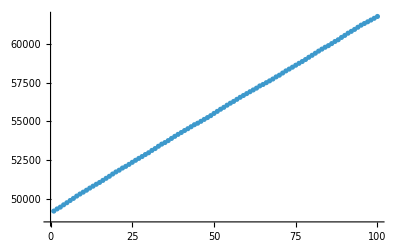

```mathematica
ListPlot[HowManyCodes5]
```

```mathematica
unknownCodes
```

48